```mathematica
Mu=0.62;   γ=5/3;

kRoss=20; (* Rosseland opacity at 0.7 Rsun*)
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
ξrad[R_,z_] = (γ-1)*χ[R,z];   (*this is what Menou and Balbus call ξrad*)

Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(kRoss*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
```

```mathematica
Ω[R_,z_]=√(7.5*10^-12);   
dLogΩdLogR=-3;   dLogΩdLogz = -3;
ΩdR[R_,z_]:=Ω[R,z]/R dLogΩdLogR;   Ωdz[R_,z_]:=Ω[R,z]/z dLogΩdLogz;
ldR[R_,z_]:=2*Ω[R,z]*R*(1+1/2 dLogΩdLogR);   ldz[R_,z_]:=Ω[R,z]*R^2/z*dLogΩdLogz;
```

```mathematica
kR[t_]:=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]:=kϕ0;
kz[t_]:=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];
k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);
```

```mathematica
DispersionRelationGS[R_,z_]:=q^3+q^2*((2*ν[R,z]*k[t]^2)/Ω[R,z]+(ξrad[R,z]*k[t]^2)/(γ*Ω[R,z]))+q*((kz[t]/k[t])^2*1/(γ*Ω[R,z]^2 ρ[R,z])*(PdR[R,z]+ρ[R,z]*Ω[R,z]^2*R-kR[t]/kz[t] Pdz[R,z])(kR[t]/kz[t] σdz[R,z]-σdR[R,z])+2/(Ω[R,z]*R)(kz[t]/k[t])^2(ldR[R,z]-kR[t]/kz[t] ldz[R,z])+2/γ*((ξrad[R,z]*k[t]^2)/Ω[R,z])((ν[R,z]*k[t]^2)/Ω[R,z])+((ν[R,z]*k[t]^2)/Ω[R,z])^2)+((kz[t]/k[t])^2*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*k[t]^2)/Ω[R,z])(PdR[R,z]+ρ[R,z]*Ω[R,z]^2*R-kR[t]/kz[t] Pdz[R,z])(kR[t]/kz[t] σdz[R,z]-σdR[R,z])+2/(γ*Ω[R,z]*R)(kz[t]/k[t])^2((ξrad[R,z]*k[t]^2)/Ω[R,z])(ldR[R,z]-kR[t]/kz[t] ldz[R,z])+1/γ((ξrad[R,z]*k[t]^2)/Ω[R,z])((ν[R,z]*k[t]^2)/Ω[R,z])^2)==0
```

```mathematica
LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]+ρ[R,z]*Ω[R,z]^2*R-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((ξrad[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((ξrad[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

ν_dyn = 17.0551, ν_rad = 1.21727, ξ_rad = 6.9*10^6, Pr = 2.7*10^-6.

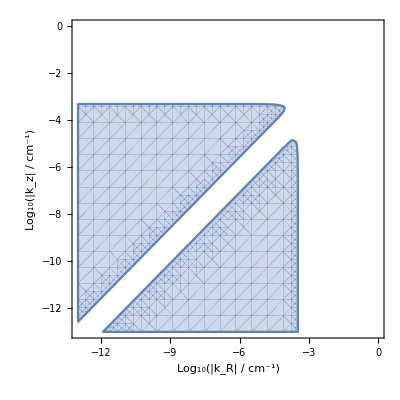

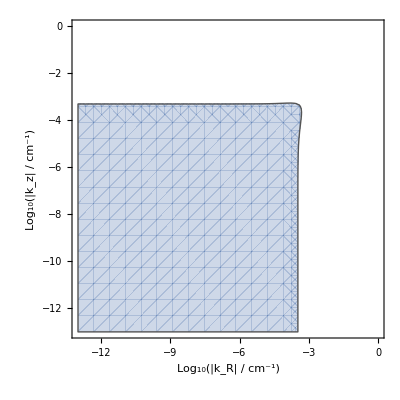

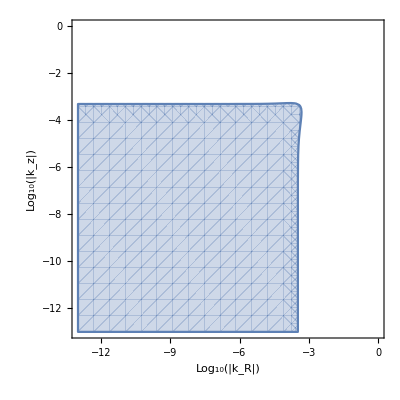

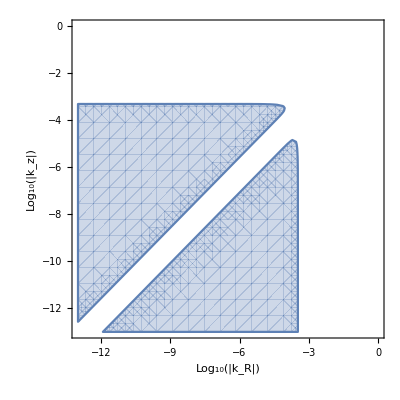

```mathematica
rper=0.65Rsun;   θper=45*Pi/180;
Rper=rper*Sin[θper];   zper=rper*Cos[θper];


"ν_dyn = "<>ToString[νdyn[Rper,zper]] <> ", ν_rad = " <> ToString[νrad[Rper,zper]] <> ", ξ_rad = " <> ToString[ScientificForm[ξrad[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> ", Pr = " <> ToString[ScientificForm[ν[Rper,zper]/ξrad[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> "."

R1at45withν=RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
R2at45withν=RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
R3at45withν=RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
R4at45withν=RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
```

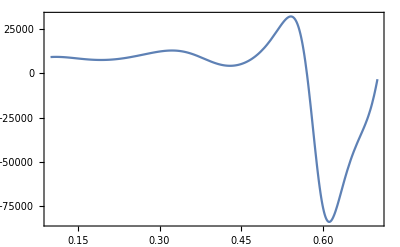

```mathematica
Plot[Min[LastTermGS[r*Rsun*Sin[Pi/4],r*Rsun*Cos[Pi/4],10^-4,-10^-5],LastTermGS[r*Rsun*Sin[Pi/4],r*Rsun*Cos[Pi/4],10^-5,-10^-4]],{r,0.1,0.7},Frame->True,PlotRange->Full]
```